```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Physical & unitful constants *)
(* Define basic constants; following Thomas's convention *)
(* lowercase >> 532, uppercase >> 1064 & superlattice *)
(* Units: 532nm = 1, hbar = 1, m_Rb = 1 *)
hbar=1.054571817*^-34;
mRb87=1.4431606*^-25;
a0=0.52917*^-10; (* Bohr radius *)
λ532=532*^-9;
λ1064=1064*^-9;
Er532=hbar^2/2/mRb87*(2*Pi/λ532)^2;
Elat532=(9/16)*Er532;
Er1064=hbar^2/2/mRb87*(2*Pi/λ1064)^2;
Elat1064=(9/16)*Er1064;(* This is questionable because we actually trap at intensity maximum, but the prefactor is calculated for intensity minimums *)
(* Some functions *)
ψ1[x_,a_]:=(1/Pi/a^2)^(1/4)*Exp[-x^2/2/a^2] (* these are states of a HO *)
ψ2[x_,a_]:=1/Sqrt[2]*(1/Pi/a^2)^(1/4)*Exp[-x^2/2/a^2]*HermiteH[1,x/a]
(* Conversion factors *)
(* Multiply numerical results by the correct units. E.g. if some variable lll = 1 has the unit of [l*t^-3], then its value in SI unit is lll*lunit*tunit^-3 *)
lunit=λ532;
munit=mRb87;
tunit=mRb87*λ532^2/hbar;
Eunit=hbar^2/λ532^2/mRb87;
JtokHz=0.001/hbar/2/Pi;  (* Multiply Joules by this to get kHz *)
(* unitless constants *)
ascat=100.4*a0 / lunit; (* s-wave scattering length *)
g3d=4*Pi*ascat; (* interaction strength in 3d *)
(* Lattice constants *)
k=2*Pi; 
K=Pi;
g=Sqrt[3]*k; (*Assuming triangular lattice*)
G=g/2;
a=2/3;
A=4/3;
k1=k*{Sqrt[3]/2,-1/2,0};
k2=k*{0,1,0};
k3=k*{-Sqrt[3]/2,-1/2,0};
K1=k1/2;
K2=k2/2;
K3=k3/2;
e1={-1/2,Sqrt[3]/2,0};
e2={1,0,0};
e3={-1/2,Sqrt[3]/2,0};
g1=k2-k3; (*g2 in ckt*)
g2=k3-k1;(*g2-g1 in ckt*)
g3=k1-k2;(*-g1 in ckt*)
G1=K2-K3;
G2=K3-K1;
G3=K1-K2;
a1=a*{0,1};
a2=a*{-Sqrt[3]/2,1/2};
a3=a*{Sqrt[3]/2,1/2};
A1=a1*2;
A2=a2*2;
A3=a3*2;
Γp={0,0};
Mp=G/2*{1,0};
Kp=G/2*{1,1/Sqrt[3]};
Cell532=2/Sqrt[27]; (* 3d, but the lattice constant in z-direction is 1 *)
Cell1064=Cell532*4;
(* Experiment parameters *)
(* I define both V532 and V1064 to be positive; signs are considered in the definition of potential functions *)
NRb=3.5*^4; (* Atom number *)
V532kHz=0;
V532=V532kHz/JtokHz/Eunit;
V1064kHz=20;
V1064=V1064kHz/JtokHz/Eunit;
VVLkHz=41;
VVL=VVLkHz/JtokHz/Eunit;
ODTx=2*Pi*23*tunit; (* 23 *)
ODTy=2*Pi*41*tunit; (* 41 *)
ODTz=2*Pi*46*tunit; (* 46 *)
ωODT=(ODTx*ODTy*ODTz)^(1/3);
aODT=Sqrt[1/ωODT];
ωVL=2*Sqrt[VVL*Er1064/Eunit];
ahoVL=Sqrt[1/ωVL];
μext=(15*NRb*ascat/aODT)^(2/5)/2*ωODT;
Rx=Sqrt[2*μext/ODTx^2];
Ry=Sqrt[2*μext/ODTy^2];
Rz=Sqrt[2*μext/ODTz^2];
Print["V1064 = ",V1064]
Print["Chemical potential = ", μext*Eunit*JtokHz, " kHz"]
Print["T-F radii (um): Rx = ", Rx*lunit*1*^6, ", Ry = ",  Ry*lunit*1*^6, ", Rz = ", Rz*lunit*1*^6, " (# of sites = ",(4*Pi/3)*Rx*Ry*Rz/Cell1064*2,")"]
Print["Peak density = ", μext/g3d/lunit^3/1*^6, " cm-3, peak atom number per site (in 1064 honeycomb lattice, no VL) = ",  4/3*μext*Rz/g3d*Cell1064/2]
```

V1064 = 48.6712

Chemical potential = 0.330337 kHz

T-F radii (um): Rx = 12.0519, Ry = 6.76084, Rz = 6.02596 (# of sites = 17744.3)

Peak density = 4.25438×10^13 cm-3, peak atom number per site (in 1064 honeycomb lattice, no VL) = 74.4737

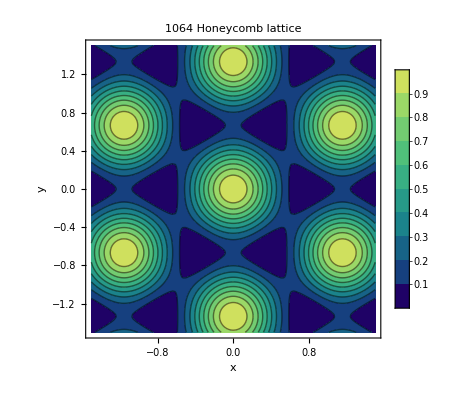

```mathematica
(* Potential definition and visualization *)
(* Bottem of the potential defined to be 0 *)
Vin532[x_,y_,δx_:0,δy_:0]:=(2/9)*(3-Cos[g1.{x-δx,y-δy,0}]-Cos[g2.{x-δx,y-δy,0}]-Cos[g3.{x-δx,y-δy,0}]);
Vout532[x_,y_,δx_:0,δy_:0]:=(1/9)*(3+2*(Cos[g1.{x-δx,y-δy,0}]+Cos[g2.{x-δx,y-δy,0}]+Cos[g3.{x-δx,y-δy,0}]));
Vin1064[x_,y_,δx_:0,δy_:0]:=1-(2/9)*(3-Cos[G1.{x-δx,y-δy,0}]-Cos[G2.{x-δx,y-δy,0}]-Cos[G3.{x-δx,y-δy,0}]);
Vout1064[x_,y_,δx_:0,δy_:0]:=1-(1/9)*(3+2*(Cos[G1.{x-δx,y-δy,0}]+Cos[G2.{x-δx,y-δy,0}]+Cos[G3.{x-δx,y-δy,0}]));
ContourPlot[Vin1064[x,y],{x,-1.5,1.5},{y,-1.5,1.5},ColorFunction->"BlueGreenYellow",FrameLabel->Automatic,PlotLegends->Automatic,PlotLabel->"1064 Honeycomb lattice"]
```

Harmonic oscillator frequency = 2π*25.8685kHz; Harmonic oscillator length in xy plane = 67.051 nm; lattice constant = 354.667 nm

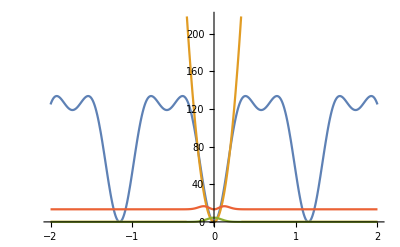

```mathematica
(* Lattice site parameters calculation *)
(* This section follows Masayuki's notes *)
Site532={0,0}; (* Vin532[Site532[[1]],Site532[[2]]] = 0 *)
Vin532cut[x_]:=V532*Vin532[x,Site532[[2]]];
ω532=Sqrt[2*V532*8/9*Pi^2/(4/Sqrt[27])^2];
aho532=Sqrt[1/ω532];
Vho[x_]:=ω532^2/2*x^2;
Bx[x_]:=UnitBox[1.5*x]
Print["Harmonic oscillator frequency = 2π*",ω532/tunit/2/Pi/1000,"kHz; Harmonic oscillator length in xy plane = ", aho532*lunit*1*^9, " nm; lattice constant = ", N[2/3*lunit*1*^9], " nm"]
Plot[{Vin532cut[x],Bx[x-Site532[[1]]]*Vho[x-Site532[[1]]],(ψ1[x-Site532[[1]],aho532]^2),(ψ2[x-Site532[[1]],aho532]^2+V532*0.1)},{x,-2,2}]
```

Harmonic oscillator frequency = 2π*5.51518kHz; Harmonic oscillator length in xy plane = 145.215 nm; lattice constant = 409.534 nm

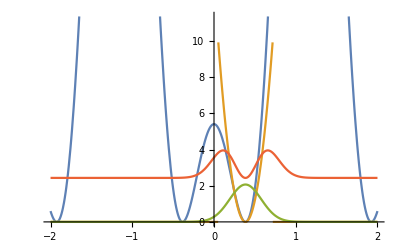

```mathematica
Site1064={2/Sqrt[27],2/3}; (* Vin1064[Site1064[[1]],Site1064[[2]]] = -1 *)
Ridge1064={0,2/3}; (* Vin1064[Ridge1064[[1]],Ridge1064[[2]]] = -8/9 *)
Vin1064cut[x_]:=V1064*Vin1064[x,Site1064[[2]]];
ω1064=Sqrt[2*V1064/9*Pi^2/(4/Sqrt[27])^2];
aho1064=Sqrt[1/ω1064];
Vho[x_]:=ω1064^2/2*x^2;
Print["Harmonic oscillator frequency = 2π*",ω1064/tunit/2/Pi/1000,"kHz; Harmonic oscillator length in xy plane = ", aho1064*lunit*1*^9, " nm; lattice constant = ", N[4/Sqrt[27]*lunit*1*^9], " nm"]
Plot[{Vin1064cut[x],Bx[x-Site1064[[1]]]*Vho[x-Site1064[[1]]],(ψ1[x-Site1064[[1]],aho1064]^2),(ψ2[x-Site1064[[1]],aho1064]^2+V1064*0.05)},{x,-2,2}]
```

```mathematica
Sorb[x_,y_,z_]:=ψ1[x,aho532]*ψ1[y,aho532]*ψ1[z,ahoVL]
U532Sband=g3d*Integrate[Abs[Sorb[x,y,z]]^4,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}];
Uformula=g3d/(Sqrt[2*Pi]^3*aho532*aho532*ahoVL);
(* s-band *)
μlat532=μext*(U532Sband/g3d*Cell532)^(2/5);
Print["-------- s-band --------"]
Print["Calculated U/g3d: ",N[U532Sband/g3d],"; μlat/μext = (U/g3d*Vsite)^(2/5) = ",(U532Sband/g3d*Cell532)^(2/5)]
Print["Check U: my U is ", U532Sband,", U from HO approximation is ", Uformula]
Print["Chemical potential with lattice: ", μlat532*Eunit*JtokHz, " kHz"]
Print["Peak atom number per site (in 1064 honeycomb lattice) = ",  μlat532/U532Sband]
Print["Sanity check: norm of Sorb = ",N[Integrate[Abs[Sorb[x,y,z]]^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}]]]
```

-------- s-band --------

Calculated U/g3d: 26.6276; μlat/μext = (U/g3d*Vsite)^(2/5) = 2.53672

Check U: my U is 3.34163, U from HO approximation is 3.34163

Chemical potential with lattice: 0.966472 kHz

Peak atom number per site (in 1064 honeycomb lattice) = 0.703837

Sanity check: norm of Sorb = 1.

```mathematica
(* Experiment parameters calculation, with lattice *)
Sorb[x_,y_,z_]:=ψ1[x,aho1064]*ψ1[y,aho1064]*ψ1[z,ahoVL]
Porb[x_,y_,z_]:=ψ1[y,aho1064]*ψ2[x,aho1064]*ψ1[z,ahoVL]
(*Grid[{{ContourPlot[Sorb[x+Site1064[[1]],y-Site1064[[1]],0],{x,-1,1},{y,-1,1}],
ContourPlot[Sorb[x-Site1064[[1]],y-Site1064[[1]],0],{x,-1,1},{y,-1,1}],
ContourPlot[Vin1064[x,y],{x,-1,1},{y,-1,1}]},{ContourPlot[Porb[x+Site1064[[1]],y-Site1064[[1]],0],{x,-1,1},{y,-1,1}],
ContourPlot[Porb[x-Site1064[[1]],y-Site1064[[1]],0],{x,-1,1},{y,-1,1}],
ContourPlot[Vin1064[x,y],{x,-1,1},{y,-1,1}]}}]*)
U1064Sband=g3d*Integrate[Abs[Sorb[x,y,z]]^4,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}];
Uformula=g3d/(Sqrt[2*Pi]^3*aho1064*aho1064*ahoVL);
U1064Pband=g3d*Integrate[Abs[Porb[x,y,z]]^4,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}];
(* s-band *)
μlat1064=μext*(U1064Sband/g3d*Cell1064/2)^(2/5);
Print["ωx/y = 2π*",ω1064/tunit/2/Pi/1000," kHz, ωz = 2π*",ωVL/tunit/2/Pi/1000," kHz"]
Print["-------- s-band --------"]
Print["Calculated U/g3d: ",N[U1064Sband/g3d],"; μlat/μext = (U/g3d*Vsite)^(2/5) = ",(U1064Sband/g3d*Cell1064/2)^(2/5)]
Print["Check U: my U is ", U1064Sband,", U from HO approximation is ", Uformula,"; "]
Print["Chemical potential with lattice: ", μlat1064*Eunit*JtokHz, " kHz"]
Print["Peak atom number per site (in 1064 honeycomb lattice) = ",  μlat1064/U1064Sband, " (not sure if there should be a factor of 2 to account for 2 sites per cell)"]
Print["Sanity check: norm of Sorb = ",N[Integrate[Abs[Sorb[x,y,z]]^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}]]]
(* p-band *)
μlat=μext*(U1064Pband/g3d*Cell1064/2)^(2/5);
Print["-------- p-band --------"]
Print["Calculated U/g3d: ",N[U1064Pband/g3d],"; μlat/μext = (U/g3d*Vsite)^(2/5) = ",(U1064Pband/g3d*Cell1064/2)^(2/5)]
Print["Chemical potential with lattice: ", μlat*Eunit*JtokHz, " kHz"]
Print["Peak atom number per site (in 1064 honeycomb lattice) = ",  μlat1064/U1064Pband, " (not sure if there should be a factor of 2 to account for 2 sites per cell)"]
Print["Sanity check: norm of Porb = ",N[Integrate[Abs[Porb[x,y,z]]^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}]]]
```

ωx/y = 2π*5.51518 kHz, ωz = 2π*18.2363 kHz

-------- s-band --------

Calculated U/g3d: 5.67702; μlat/μext = (U/g3d*Vsite)^(2/5) = 1.80385

Check U: my U is 0.712439, U from HO approximation is 0.712439;

Chemical potential with lattice: 0.687253 kHz

Peak atom number per site (in 1064 honeycomb lattice) = 2.34753 (not sure if there should be a factor of 2 to account for 2 sites per cell)

Sanity check: norm of Sorb = 1.

-------- p-band --------

Calculated U/g3d: 4.25776; μlat/μext = (U/g3d*Vsite)^(2/5) = 1.60777

Chemical potential with lattice: 0.61255 kHz

Peak atom number per site (in 1064 honeycomb lattice) = 3.13004 (not sure if there should be a factor of 2 to account for 2 sites per cell)

Sanity check: norm of Porb = 1.

```mathematica
t1064Pband=-NIntegrate[Porb[x+Site1064[[1]],y-Site1064[[1]],z]*(-D[Porb[x-Site1064[[1]],y-Site1064[[1]],z],x,x]/2-D[Porb[x-Site1064[[1]],y-Site1064[[1]],z],y,y]/2-D[Porb[x-Site1064[[1]],y-Site1064[[1]],z],z,z]/2+Vin1064[x,y]*Porb[x-Site1064[[1]],y-Site1064[[1]],z]),{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}] (* Adding an offset to Vin1064 changes t, which doesn't make sense *)(*Need to add z lattice*)
```

8.38756

```mathematica
ahoVL*lunit
```

7.98588×10^-8